# Lab 1: Introduction Assignment

### Instructions

Welcome to your first Lab Assignment. The purpose of this assignment is to assess your knowledge of the basics of Mathematica. Please refer to “Lab 1 Introduction” if you have problems with any of the questions. Here are some things to remember as you complete this first assignment:
1. Save the notebook to your computer right away, and save your work often.
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Question 1: Using Cells

a) Right below this cell create a text cell. In the text cell, type your first and last name.

Caleb Jacobs

b) Click below and open a math input cell. In it, take the number of letters in your last name and subtract the number of letters in your first name. Evaluate the cell and show the output.

```mathematica
StringLength["Jacobs"]-StringLength["Caleb"]
```

1

### Question 2: Free Form Input

a) I would like to find out some local information about Houghton MI. Using the free form entry cell, type in “Houghton MI” and evaluate. The plus sign in the free form entry box will open and close additional information about your search. Open the additional information and read through it to find whatever you are most interested in. Click on the table, graph, or item that you find most interesting to highlight it and then type shift+enter to select it. Finally, click the subtraction sign to close the additional information so that only your topic of interest is displaying.

WolframAlphaQueryResults

-Graphics-(based on current OpenStreetMap data)

b) Now I am interested in the distance from the earth to the moon. Using free form entry, enter in “distance to the moon” and repeat the steps in part “a”, i.e. expand to see the additional information, highlight your favorite pod by clicking on it, choose it by typing shift+enter, and then close the additional information.

WolframAlphaQueryResults

-Graphics-(from Oct 18, 2017 to Apr 18, 2018) | (in thousands of miles)

### Question 3: Help Menu

a) Using the documentation center, research the command “Solve.” Copy the code from the first example presented under the “Examples” section in the documentation center and paste it directly below in a math input cell.

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

b) Copy the code from part a into a new math input cell below. Modify the code to solve the polynomial 2 x^2+4x-2=0.

```mathematica
Solve[2 x^2+4x-2==0,x]
```

{{x→-1-√2},{x→-1+√2}}

c) Use the documentation center to research the command “Log.” In a new math input cell below, calculate the numerical value of ln(5) (as usual, by ln we mean the natural logarithm). Present your answer as a decimal.

```mathematica
Log[5]//N
```

1.60944

### Question 4: Mathematica Syntax

a) Create a text cell directly below each math input cell that describes the error in the following examples.

```mathematica
cos[2]
```

cos[2]

The function is not capitalized

```mathematica
Plot[Sin(x),{x,-2,2}]
```

-Graphics-

The Sin function is using parentheses for the argument rather then brackets

```mathematica
N[pi,15]
```

pi

π should be capitalized

### Question 5: Visualizations

a) Define plot1, plot2, and plot3 (or any other variable names) to be the plots of the functions sin(x), sin(x)+2, and sin(x)+4 from x=-2π  to x=2π respectively.

```mathematica
plot1 = Plot[Sin[x],{x,-2π,2π}];
plot2 = Plot[Sin[x]+2,{x,-2π,2π}];
plot3 = Plot[Sin[x]+4,{x,-2π,2π}];
```

b) Use the Show command to display the three plots together on one graph. Note: to see all the functions properly you will need to use the PlotRange option. Refer to the Documentation Center if you need help with this option.

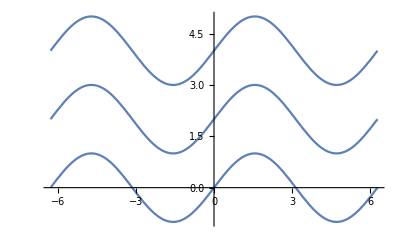

```mathematica
Show[plot1,plot2,plot3,PlotRange->{{-2π,2π},{-1,5}}]
```

c) Create a text cell directly below this cell and describe what the plot of sin(x)+b would look like if b was some positive number.

The plot would be a sin function with a vertical translation up by “b.”